# Bs2JpsiPhi phenomenology

## Marcos Romero Lamas (mromerol@cern.ch)

## Ingredients for de model

## Time evolution model

```mathematica
Clear[ta,tb,tc,td]
ta[t_,Γ_,ΔΓ_,Δm_]:=Exp[-Γ*t]*Cosh[ΔΓ*t/2];
tb[t_,Γ_,ΔΓ_,Δm_]:=Exp[-Γ*t]*Sinh[ΔΓ*t/2];
tc[t_,Γ_,ΔΓ_,Δm_]:=Exp[-Γ*t]*Cos[Δm*t];
td[t_,Γ_,ΔΓ_,Δm_]:=Exp[-Γ*t]*Sin[Δm*t];
```

## Coefficients for the amplitudes

```mathematica
Clear[nk]
nk[k_,A0_,AS_,Apar_,Aper_,CSP_]:=A0*A0/;k==1;
nk[k_,A0_,AS_,Apar_,Aper_,CSP_]:=Apar*Apar/;k==2;
nk[k_,A0_,AS_,Apar_,Aper_,CSP_]:=Aper*Aper/;k==3;
nk[k_,A0_,AS_,Apar_,Aper_,CSP_]:=Aper*Apar/;k==4;
nk[k_,A0_,AS_,Apar_,Aper_,CSP_]:=A0*Apar/;k==5;
nk[k_,A0_,AS_,Apar_,Aper_,CSP_]:=A0*Aper/;k==6;
nk[k_,A0_,AS_,Apar_,Aper_,CSP_]:=AS*AS/;k==7;
nk[k_,A0_,AS_,Apar_,Aper_,CSP_]:=CSP*AS*Apar/;k==8;
nk[k_,A0_,AS_,Apar_,Aper_,CSP_]:=CSP*AS*Aper/;k==9;
nk[k_,A0_,AS_,Apar_,Aper_,CSP_]:=CSP*AS*A0/;k==10;
```

## Coefficients for the angular part

```mathematica
Clear[fk,innerfk]
innerfk[k_,CosK_,SinK_,CosL_,SinL_,CosP_,SinP_]:=CosK*CosK*SinL*SinL/;k==1
innerfk[k_,CosK_,SinK_,CosL_,SinL_,CosP_,SinP_]:=(1/2)*SinK*SinK*(1.-CosP*CosP*SinL*SinL)/;k==2
innerfk[k_,CosK_,SinK_,CosL_,SinL_,CosP_,SinP_]:=(1/2)*SinK*SinK*(1.-SinP*SinP*SinL*SinL)/;k==3
innerfk[k_,CosK_,SinK_,CosL_,SinL_,CosP_,SinP_]:=SinK*SinK*SinL*SinL*SinP*CosP/;k==4
innerfk[k_,CosK_,SinK_,CosL_,SinL_,CosP_,SinP_]:=+Sqrt[2]*SinK*CosK*SinL*CosL*CosP/;k==5
innerfk[k_,CosK_,SinK_,CosL_,SinL_,CosP_,SinP_]:=-Sqrt[2]*SinK*CosK*SinL*CosL*SinP/;k==6
innerfk[k_,CosK_,SinK_,CosL_,SinL_,CosP_,SinP_]:=SinL*SinL/3/;k==7
innerfk[k_,CosK_,SinK_,CosL_,SinL_,CosP_,SinP_]:=+2*SinK*SinL*CosL*CosP/Sqrt[6]/;k==8
innerfk[k_,CosK_,SinK_,CosL_,SinL_,CosP_,SinP_]:=-2*SinK*SinL*CosL*SinP/Sqrt[6]/;k==9
innerfk[k_,CosK_,SinK_,CosL_,SinL_,CosP_,SinP_]:=+2*CosK*SinL*SinL/Sqrt[3]/;k==10

fk[k_,CosK_,CosL_,Phi_]:=Module[
{SinK=Sqrt[1-CosK*CosK],SinL=Sqrt[1-CosL*CosL],SinP=Sin[-Phi],CosP=Cos[-Phi]},
innerfk[k,CosK,SinK,CosL,SinL,CosP,SinP]
]
```

## Coefficients for the time dependent part

```mathematica
Clear[ak]
ak[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+(1/2)*(1.+λ0*λ0)/;k==1
ak[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+(1/2)*(1.+λpar*λpar)/;k==2
ak[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+(1/2)*(1.+λper*λper)/;k==3
ak[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+(1/2)*(Sin[δper-δpar]-λper*λpar*Sin[δper-δpar-ϕper+ϕpar])/;k==4
ak[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+(1/2)*(Cos[δ0-δpar]+λ0*λpar*Cos[δ0-δpar-ϕ0+ϕpar])/;k==5
ak[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-(1/2)*(Sin[δ0-δper]-λ0*λper*Sin[δ0-δper-ϕ0+ϕper])/;k==6
ak[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+(1/2)*(1.+λS*λS)/;k==7
ak[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+(1/2)*(Cos[δS-δpar]-λS*λpar*Cos[δS-δpar-ϕS+ϕpar])/;k==8
ak[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-(1/2)*(Sin[δS-δper]+λS*λper*Sin[δS-δper-ϕS+ϕper])/;k==9
ak[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+(1/2)*(Cos[δS-δ0]-λS*λ0*Cos[δS-δ0-ϕS+ϕ0])/;k==10
```

```mathematica
Clear[bk]
bk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-λ0*Cos[ϕ0]/;k==1
bk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-λpar*Cos[ϕpar]/;k==2
bk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+λper*Cos[ϕper]/;k==3
bk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=(1/2)*(λper*Sin[δper-δpar-ϕper]+λpar*Sin[δpar-δper-ϕpar])/;k==4
bk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-(1/2)*(λ0*Cos[δ0-δpar-ϕ0]+λpar*Cos[δpar-δ0-ϕpar])/;k==5
bk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=(1/2)*(λ0*Sin[δ0-δper-ϕ0]+λper*Sin[δper-δ0-ϕper])/;k==6
bk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=λS*Cos[ϕS]/;k==7
bk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=(1/2)*(λS*Cos[δS-δpar-ϕS]-λpar*Cos[δpar-δS-ϕpar])/;k==8
bk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-(1/2)*(λS*Sin[δS-δper-ϕS]-λper*Sin[δper-δS-ϕper])/;k==9
bk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=(1/2)*(λS*Cos[δS-δ0-ϕS]-λ0*Cos[δ0-δS-ϕ0])/;k==10
```

```mathematica
Clear[ck]
ck[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+(1/2)*(1.-λ0*λ0)/;k==1
ck[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+(1/2)*(1.-λpar*λpar)/;k==2
ck[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+(1/2)*(1.-λper*λper)/;k==3
ck[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=+(1/2)*(Sin[δper-δpar]-λper*λpar*Sin[δper-δpar-ϕper+ϕpar])/;k==4
ck[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=(1/2)*(Cos[δ0-δpar]-λ0*λpar*Cos[δ0-δpar-ϕ0+ϕpar])/;k==5
ck[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-(1/2)*(Sin[δ0-δper]+λ0*λper*Sin[δ0-δper-ϕ0+ϕper])/;k==6
ck[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=(1/2)*(1.-λS*λS)/;k==7
ck[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=(1/2)*(Cos[δS-δpar]+λS*λpar*Cos[δS-δpar-ϕS+ϕpar])/;k==8
ck[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-(1/2)*(Sin[δS-δper]-λS*λper*Sin[δS-δper-ϕS+ϕper])/;k==9
ck[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=(1/2)*(Cos[δS-δ0]+λS*λ0*Cos[δS-δ0-ϕS+ϕ0])/;k==10
```

```mathematica
Clear[dk]
dk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=λ0*Sin[ϕ0]/;k==1
dk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=λpar*Sin[ϕpar]/;k==2
dk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-λper*Sin[ϕper]/;k==3
dk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-(1/2)*(λper*Cos[δper-δpar-ϕper]+λpar*Cos[δpar-δper-ϕpar])/;k==4
dk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-(1/2)*(λ0*Sin[δ0-δpar-ϕ0]+λpar*Sin[δpar-δ0-ϕpar])/;k==5
dk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-(1/2)*(λ0*Cos[δ0-δper-ϕ0]+λper*Cos[δper-δ0-ϕper])/;k==6
dk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-λS*Sin[ϕS]/;k==7
dk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=(1/2)*(λS*Sin[δS-δpar-ϕS]-λpar*Sin[δpar-δS-ϕpar])/;k==8
dk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=-(1/2)*(-λS*Cos[δS-δper-ϕS]+λper*Cos[δper-δS-ϕper])/;k==9
dk[k_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=(1/2)*(λS*Sin[δS-δ0-ϕS]-λ0*Sin[δ0-δS-ϕ0])/;k==10
```

## Building the full p.d.f. model

```mathematica
Clear[hk,hkbar,pdfB,pdfBbar,pdfB,FullPDF](**)
hk[t_,k_,Γ_,ΔΓ_,Δm_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=(3/(4*Pi))*(
ta[t,Γ,ΔΓ,Δm]*ak[k,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper]+tb[t,Γ,ΔΓ,Δm]*bk[k,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper]+tc[t,Γ,ΔΓ,Δm]*ck[k,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper]+td[t,Γ,ΔΓ,Δm]*dk[k,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper]
)
hkbar[t_,k_,Γ_,ΔΓ_,Δm_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_]:=(3/(4*Pi))*(
ta[t,Γ,ΔΓ,Δm]*ak[k,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper]+tb[t,Γ,ΔΓ,Δm]*bk[k,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper]-tc[t,Γ,ΔΓ,Δm]*ck[k,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper]-td[t,Γ,ΔΓ,Δm]*dk[k,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper]
)
```

```mathematica
pdfB[       t_,CosK_,CosL_,Phi_,k_,Γ_,ΔΓ_,Δm_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_,A0_,AS_,Apar_,Aper_,CSP_]:=nk[k,A0,AS,Apar,Aper,CSP]*hk[t,k,Γ,ΔΓ,Δm,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper]*fk[k,CosK,CosL,Phi];
pdfBbar[t_,CosK_,CosL_,Phi_,k_,Γ_,ΔΓ_,Δm_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_,A0_,AS_,Apar_,Aper_,CSP_]:=nk[k,A0,AS,Apar,Aper,CSP]*hkbar[t,k,Γ,ΔΓ,Δm,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper]*fk[k,CosK,CosL,Phi];
```

```mathematica
FullPDF[t_,CosK_,CosL_,Phi_,k_,Γ_,ΔΓ_,Δm_,ϕ0_,ϕS_,ϕpar_,ϕper_,δ0_,δS_,δpar_,δper_,λ0_,λS_,λpar_,λper_,A0_,AS_,Apar_,Aper_,CSP_]:=Bevts*pdfB[          t,CosK,CosL,Phi,k,Γ,ΔΓ,Δm,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper,A0,AS,Apar,Aper,CSP]+Bbevts*pdfBbar[t,CosK,CosL,Phi,k,Γ,ΔΓ,Δm,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper,A0,AS,Apar,Aper,CSP]
```

```mathematica
FullPDFAllTerms=Sum[
FullPDF[t,CosK,CosL,Phi,k,Γ,ΔΓ,Δm,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper,A0,AS,Apar,Aper,CSP],
{k,1,10}];
```

```mathematica
Table[
{fk[k,cK,cL,phi],nk[k,A0,AS,Apar,Aper,CSP],ak[k,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper],bk[k,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper],ck[k,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper],dk[k,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper]}
,{k,1,10}]//MatrixForm
```

(cK^2 (1-cL^2) | A0^2 | 1/2 (1.+λ0^2) | -λ0 Cos[ϕ0] | 1/2 (1.-λ0^2) | λ0 Sin[ϕ0]
1/2 (1-cK^2) (1.-(1-cL^2) Cos[phi]^2) | Apar^2 | 1/2 (1.+λpar^2) | -λpar Cos[ϕpar] | 1/2 (1.-λpar^2) | λpar Sin[ϕpar]
1/2 (1-cK^2) (1.-(1-cL^2) Sin[phi]^2) | Aper^2 | 1/2 (1.+λper^2) | λper Cos[ϕper] | 1/2 (1.-λper^2) | -λper Sin[ϕper]
-((1-cK^2) (1-cL^2) Cos[phi] Sin[phi]) | Apar Aper | 1/2 (-Sin[δpar-δper]+λpar λper Sin[δpar-δper-ϕpar+ϕper]) | 1/2 (λpar Sin[δpar-δper-ϕpar]-λper Sin[δpar-δper+ϕper]) | 1/2 (-Sin[δpar-δper]+λpar λper Sin[δpar-δper-ϕpar+ϕper]) | 1/2 (-λpar Cos[δpar-δper-ϕpar]-λper Cos[δpar-δper+ϕper])
√2 cK √(1-cK^2) cL √(1-cL^2) Cos[phi] | A0 Apar | 1/2 (Cos[δ0-δpar]+λ0 λpar Cos[δ0-δpar-ϕ0+ϕpar]) | 1/2 (-λ0 Cos[δ0-δpar-ϕ0]-λpar Cos[δ0-δpar+ϕpar]) | 1/2 (Cos[δ0-δpar]-λ0 λpar Cos[δ0-δpar-ϕ0+ϕpar]) | 1/2 (-λ0 Sin[δ0-δpar-ϕ0]+λpar Sin[δ0-δpar+ϕpar])
√2 cK √(1-cK^2) cL √(1-cL^2) Sin[phi] | A0 Aper | 1/2 (-Sin[δ0-δper]+λ0 λper Sin[δ0-δper-ϕ0+ϕper]) | 1/2 (λ0 Sin[δ0-δper-ϕ0]-λper Sin[δ0-δper+ϕper]) | 1/2 (-Sin[δ0-δper]-λ0 λper Sin[δ0-δper-ϕ0+ϕper]) | 1/2 (-λ0 Cos[δ0-δper-ϕ0]-λper Cos[δ0-δper+ϕper])
1/3 (1-cL^2) | AS^2 | 1/2 (1.+λS^2) | λS Cos[ϕS] | 1/2 (1.-λS^2) | -λS Sin[ϕS]
√(2/3) √(1-cK^2) cL √(1-cL^2) Cos[phi] | Apar AS CSP | 1/2 (Cos[δpar-δS]-λpar λS Cos[δpar-δS-ϕpar+ϕS]) | 1/2 (-λpar Cos[δpar-δS-ϕpar]+λS Cos[δpar-δS+ϕS]) | 1/2 (Cos[δpar-δS]+λpar λS Cos[δpar-δS-ϕpar+ϕS]) | 1/2 (-λpar Sin[δpar-δS-ϕpar]-λS Sin[δpar-δS+ϕS])
√(2/3) √(1-cK^2) cL √(1-cL^2) Sin[phi] | Aper AS CSP | 1/2 (Sin[δper-δS]+λper λS Sin[δper-δS-ϕper+ϕS]) | 1/2 (λper Sin[δper-δS-ϕper]+λS Sin[δper-δS+ϕS]) | 1/2 (Sin[δper-δS]-λper λS Sin[δper-δS-ϕper+ϕS]) | 1/2 (-λper Cos[δper-δS-ϕper]+λS Cos[δper-δS+ϕS])
(2 cK (1-cL^2))/(√3) | A0 AS CSP | 1/2 (Cos[δ0-δS]-λ0 λS Cos[δ0-δS-ϕ0+ϕS]) | 1/2 (-λ0 Cos[δ0-δS-ϕ0]+λS Cos[δ0-δS+ϕS]) | 1/2 (Cos[δ0-δS]+λ0 λS Cos[δ0-δS-ϕ0+ϕS]) | 1/2 (-λ0 Sin[δ0-δS-ϕ0]-λS Sin[δ0-δS+ϕS]))

```mathematica
DiffRateIntegral=
Total[
Table[
Integrate[
FullPDF[t,CosK,CosL,Phi,k,Γ,ΔΓ,Δm,ϕ0,ϕS,ϕpar,ϕper,δ0,δS,δpar,δper,λ0,λS,λpar,λper,A0,AS,Apar,Aper,CSP],
{t,0,15},{Phi,-Pi,Pi},{CosL,-1,1}]
,{k,1,10}]
];
```

## Play with some parameters

```mathematica
params={
ΔΓ->0.09025,Δm->17.7,Γ->0.6613,
ϕ0->-0.03,ϕS->-0.03+Pi,ϕpar->-0.03,ϕper->-0.03,
δ0->0,δS->1.877+3.2038,δpar->3.033,δper->3.2038,
λ0->1,λS->1,λpar->1,λper->1,
A0->0.350027199,AS->0.79270952989,Apar->0.23609379,Aper->0.25135944,
CSP->0.870952989757,
Bevts->0,Bbevts->0.5
};
```

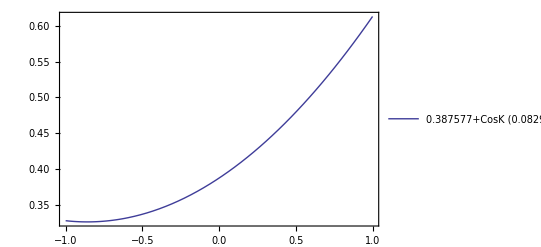

```mathematica
Plot[{
DiffRateIntegral/.params
},{CosK,-1,1}
,PlotRange->All,Frame->True,PlotTheme->"Classic",PlotLegends->{FullSimplify[DiffRateIntegral/.params]}]
```